```mathematica
<<MaTeX`
```

#### Задача 2

```mathematica
Manipulate[Plot[{x Tan[x],√(A^2-x^2)},{x,0,10},PlotRange->{{0,10},{0,15}}],{A,0,20}]
```

```mathematica
Manipulate[Plot[{ x Cot[x],-√(A^2-x^2)},{x,0,10},PlotRange->{{0,10},{-10,10}}],{A,0,20}]
```

#### Задача 4

```mathematica
ClearAll[e,k,k1,ampT,ampR,a]
h=1;
k[α_]=(√(2 α))/h;
k1[α_]=(√(2(α-1)))/h;
ampT[α_,a_]=(4 k[α]^2 k1[α]^2)/(4 k[α]^2 k1[α]^2+(k1[α]^2-k[α]^2)^2 Sin[k1[α] a]^2);
ampR[α_,a_]=((k1[α]^2-k[α]^2)^2 Sin[k1[α] a]^2)/(4 k[α]^2 k1[α]^2+(k1[α]^2-k[α]^2)^2 Sin[k1[α] a]^2);
Manipulate[Plot[{ampT[α,a], ampR[α,a]},{α,0,2.5},PlotRange->{{0,2.5},{-0.04,1.01}},AxesLabel->MaTeX@{"E/V_0","T, R"},Epilog->{Dashed,Line[{{1,0},{1,1},{2.5,1}}]},PlotLegends->MaTeX@{"T\\left(E/V_0\\right)","R\\left(E/V_0\\right)"},GridLines->{Table[1+(π^2 n^2 h^2)/(2 a^2),{n,10}],{}},ImageSize->500],{a,0.01,20}]
```

#### Задача 5

```mathematica
Manipulate[Plot[{x/A,1+ⅇ^(-2x) },{x,0,10},PlotRange->All],{A,0.1,20}]
```

```mathematica
Manipulate[Plot[{x/A,1-ⅇ^(-2x) },{x,0,1},PlotRange->All],{A,0.1,20}]
```

```mathematica
Integrate[Cosh[k x]^2,{x,0,a}]
```

(2 a k+Sinh[2 a k])/(4 k)

```mathematica
Integrate[ⅇ^(-2 k x),{x,a,+Infinity}]
```

ConditionalExpression[ⅇ^(-2 a k)/(2 k), Re[k]>0]

#### Задача 6

```mathematica
Manipulate[Plot[{Cos[p]-A/p Sin[p],1,-1},{p,-7,15},GridLines->{{3.1415,2.3311,-2.3311,5.95017},{}},PlotRange->All],{A,0.9,3}]
```

```mathematica
Manipulate[Plot[{Cos[p]-A/p Sin[p],1,-1},{p,0,20},PlotRange->{{0,20},{-7,7}},GridLines->{Table[π n,{n,10}],{}}],{A,50,100}]
```

```mathematica
Manipulate[Plot[{Cos[k]-a/k Sin[k],1,-1},{k,-30,30}],{a,0,10}]
```

```mathematica
func[a_,aqq_]:={
k=Range[-10,10,aqq];
kappa=Range[-5,5,aqq/10];
q={};
e={};
If[-1<=Cos[#]-a/# Sin[#]<=1,
cosQ=ArcCos[Cos[#]-a/# Sin[#]];
AppendTo[q,cosQ];
AppendTo[q,-cosQ];
AppendTo[e,#^2];
AppendTo[e,#^2];
]&/@k;
If[-1<=Cosh[#]-a/# Sinh[#]<=1,
cosQ=ArcCos[Cosh[#]-a/# Sinh[#]];
AppendTo[q,cosQ];
AppendTo[q,-cosQ];
AppendTo[e,-#^2];
AppendTo[e,-#^2];
]&/@kappa;
Show[{ListPlot[{Transpose[{q,e}]},PlotStyle->{PointSize->0.005},PlotRange->{{-3.1,3.1},{-10,100}}],Graphics[Text[MaTeX@{"A="+a},{2,40}]],Plot[{k^2,(k-(2π)/1)^2,(k+(2π)/1)^2},{k,-π,π},PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed}}]},ImageSize->Large]}
```

```mathematica
Manipulate[func[a,0.009],{a,{0.1,1,1.8,2,2.2,3,10,30}}]
```

```mathematica
DynamicModule[{a=10},func[a,0.009]]
```

ЗАДАЧА 19

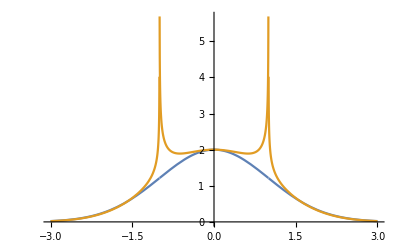

```mathematica
ψ[x_]:=Piecewise[{{Exp[-Abs[π/4+1/2 (x Sqrt[1-x^2]+ArcSin[x])]]/(Abs[1-x^2])^(1/4),x<-1},{(2 Cos[1/2 (x Sqrt[1-x^2]+ArcSin[x])])/(Abs[1-x^2])^(1/4),-1<=x<=1},{Exp[-Abs[1/2 (x Sqrt[1-x^2]-ArcCos[x])]]/(Abs[1-x^2])^(1/4),x>=1}},x];
Plot[{2 E^(-x^2/2),ψ[x]},{x,-3,3}]
```

ЗАДАЧА 14*

```mathematica
sol=NDSolve[{I D[u[t,x],t]==-1/2 Laplacian[u[t,x],{x}]+200 x u[t,x],u[0,x]==Sqrt[2] Sin[π x],u[t,0]==0,u[t,1]==0},u[t,x],{t,0,0.5},{x,0,1}];
Plot3D[Evaluate[(Abs@u[t,x])^2/. %],{t,0,0.5},{x,0,1},PlotRange->All]
NIntegrate[Abs[(u[t,x]/. sol/. {t->0.5})[[1]]]^2,{x,0,1}]
```

-Graphics3D-

1.00065